```mathematica
(* SOLVE FHN ODE MODEL *)
```

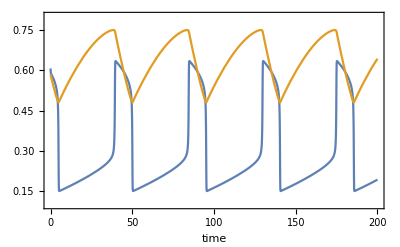

```mathematica
udot=-u^3+c u^2+d u-v;
vdot=ϵ(u-b v+a);
coef={a->-0.85,b->0.05,c->1.2,d->0.5,ϵ->0.01};
sol=NDSolve[{u'[t]==Evaluate[udot/.{u->u[t],v->v[t]}]/.coef,v'[t]==Evaluate[vdot/.{u->u[t],v->v[t]}]/.coef,u[0]==-0.6,v[0]==0.2},{u[t],v[t]},{t,0,2000}][[1]];
fig=Plot[Evaluate[{-0.21u[t]+0.48,0.32v[t]+0.52}/.sol/.t->5.75t],{t,0,200},Frame->True,PlotRange->{0.1,0.8},FrameStyle->14,FrameLabel->{"time"}]
```